```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["mesh2x5.txt","Table"];
nElements = data⟦1,1⟧
nPoints=data⟦1,2⟧
elements = Table[data⟦i⟧,{i,2,1+nElements}];
points = Table[data⟦i⟧,{i,2+nElements, 1 + nElements + nPoints}];
picElements[i_]:=ListLinePlot[Append[Table[points⟦elements⟦i,j⟧+1⟧,{j,1,6}],points⟦elements⟦i,1⟧+1⟧]]
x = Transpose[points][[1]];
y= Transpose[points][[2]];
{minx, maxx}={Min[x],Max[x]}
{miny, maxy}={Min[y],Max[y]}
```

22

62

{0.,24.0833}

{-3.99863,18.2014}

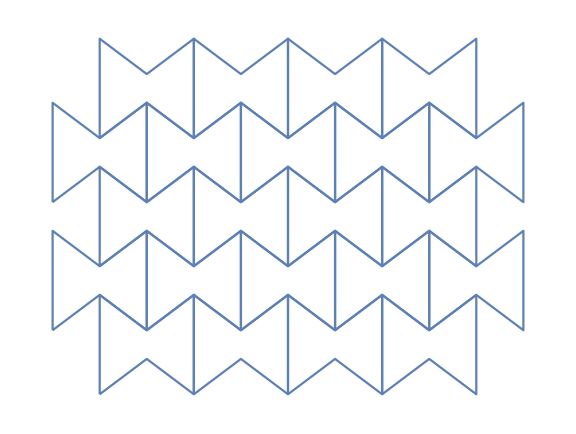

```mathematica
pic=Show[Table[picElements[i],{i,1,nElements}],PlotRange->{{minx,maxx},{miny,maxy}},Axes->{False,False},AxesOrigin->{0,0},AspectRatio->maxy/maxx,ImageSize->Large]
```

```mathematica
Export["2x5.jpg",pic]
```

2x5.jpg